```mathematica
Table[Binomial[n,2],{n,10}]
```

{0,1,3,6,10,15,21,28,36,45}

```mathematica
Asymptotic[Binomial[n,2],n->∞]
```

n^2/2

```mathematica
NSolve[n^2/2==100,n]
```

{{n→-14.1421},{n→14.1421}}

```mathematica
Dataset[Table[{n,Binomial[n,2]},{n,Join[Range[5],{10,15,20}]}]]
```

Two options are considered for an engine part:

A complete in-house manufacturing, with initial equipment cost of 50k, labor cost of 26k, material cost of 10 per engine part.

partial manufacture that is partially finished engine parts are purchased with initial equipment cost of 35k, labor cost of 10k per year, material cost of 3 per engine part, and an additional cost of 40 per partially finished engine part.

```mathematica
ToAnnualPaymentFromPresent[50k,1.1,6]
```

11480.4

```mathematica
eqn=-ToAnnualPaymentFromPresent[50k,1.1,6]-26k-10x==-ToAnnualPaymentFromPresent[35k,1.1,6]-10k-3x-40x
```

-37480.4-10 x==-18036.3-43 x

```mathematica
Solve[eqn,x]
```

{{x→589.215}}

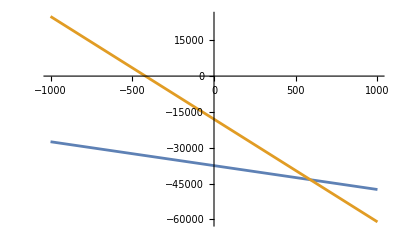

```mathematica
Plot[{-ToAnnualPaymentFromPresent[50k,1.1,6]-26k-10x,-ToAnnualPaymentFromPresent[35k,1.1,6]-10k-3x-40x},{x,-1k,k}]
```